Clear

-0.86476

0.30804

-0.0101277

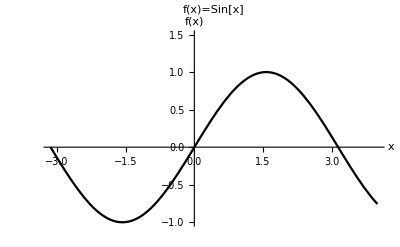

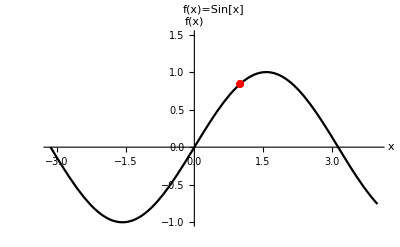

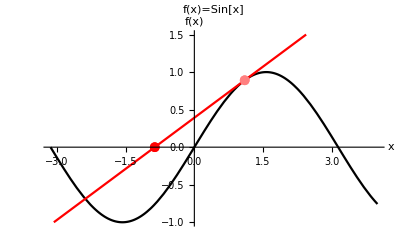

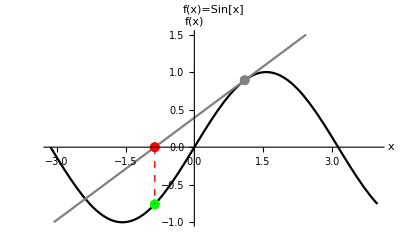

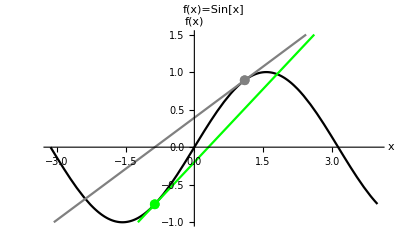

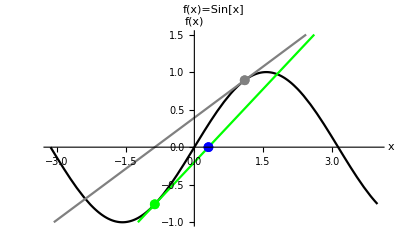

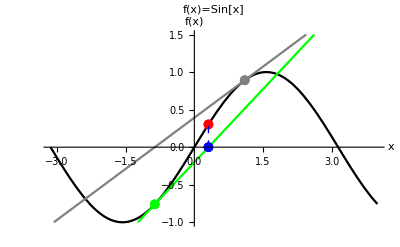

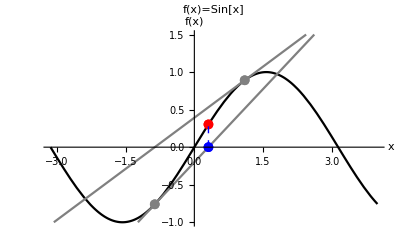

```mathematica
Clear
x0 = 1;
x1=x0-Sin[x0]/Cos[x0]//N
x2=x1-Sin[x1]/Cos[x1]//N
x3=x2-Sin[x2]/Cos[x2]//N
(*1*)
Plot[Sin[x],{x,-π,4},PlotStyle->{Black},PlotLabel->"f(x)=Sin[x]",AxesLabel->{"x","f(x)"},PlotRange->{{-π,4},{-1,1.5}}]
(*2*)
Show[Plot[Sin[x],{x,-π,4},PlotStyle->Black,PlotLabel->"f(x)=Sin[x]",AxesLabel->{"x","f(x)"},PlotRange->{{-π,4},{-1,1.5}}],ListPlot[{{1,Sin[1]}},PlotMarkers->{"●",8},PlotStyle->Red]]
(*3*)
Show[Plot[{Sin[x],Sin[x0]+Cos[x0]*(x-x0)},{x,-π,4},PlotStyle->{Black,Red},PlotLabel->"f(x)=Sin[x]",AxesLabel->{"x","f(x)"},PlotRange->{{-π,4},{-1,1.5}}],ListPlot[{{{x0,Sin[x0]}},{{x1,0}}},PlotMarkers->{{●,10},{●,10}},PlotStyle->{Pink,Red}]]
(*4*)
Show[Plot[{Sin[x],Sin[x0]+Cos[x0]*(x-x0)},{x,-π,4},PlotStyle->{Black,Gray},PlotLabel->"f(x)=Sin[x]",AxesLabel->{"x","f(x)"},PlotRange->{{-π,4},{-1,1.5}}],ListPlot[{{{x0,Sin[x0]}},{{x1,0}},{{x0-Sin[x0]/Cos[x0],Sin[x0-Sin[x0]/Cos[x0]]}}},PlotMarkers->{{●,10},{●,10},{●,10}},PlotStyle->{Gray,Red,Green}],Graphics[{Dashed,Red,Line[{{x1,0},{x1,Sin[x1]}}]}]]
(*5*)
Show[Plot[{Sin[x],Sin[x0]+Cos[x0]*(x-x0),Sin[x1]+Cos[x1]*(x-(x1))},{x,-π,4},PlotStyle->{Black,Gray,Green},PlotLabel->"f(x)=Sin[x]",AxesLabel->{"x","f(x)"},PlotRange->{{-π,4},{-1,1.5}}],ListPlot[{{{x0,Sin[x0]}},{{x0-Sin[x0]/Cos[x0],Sin[x0-Sin[x0]/Cos[x0]]}}},PlotMarkers->{{●,10},{●,10}},PlotStyle->{Gray,Green}]]
(*5*)
Show[Plot[{Sin[x],Sin[x0]+Cos[x0]*(x-x0),Sin[x1]+Cos[x1]*(x-(x1))},{x,-π,4},PlotStyle->{Black,Gray,Green},PlotLabel->"f(x)=Sin[x]",AxesLabel->{"x","f(x)"},PlotRange->{{-π,4},{-1,1.5}}],ListPlot[{{{x0,Sin[x0]}},{{x0-Sin[x0]/Cos[x0],Sin[x0-Sin[x0]/Cos[x0]]}},{{x2,0}}},PlotMarkers->{{●,10},{●,10},{●,10}},PlotStyle->{Gray,Green,Blue}]]
(*6*)
Show[Plot[{Sin[x],Sin[x0]+Cos[x0]*(x-x0),Sin[x1]+Cos[x1]*(x-(x1))},{x,-π,4},PlotStyle->{Black,Gray,Green},PlotLabel->"f(x)=Sin[x]",AxesLabel->{"x","f(x)"},PlotRange->{{-π,4},{-1,1.5}}],ListPlot[{{{x0,Sin[x0]}},{{x0-Sin[x0]/Cos[x0],Sin[x0-Sin[x0]/Cos[x0]]}},{{x2,0}},{{x2,Sin[x2]}}},PlotMarkers->{{●,10},{●,10},{●,10}},PlotStyle->{Gray,Green,Blue,Red,Red}],Graphics[{Dashed,Blue,Line[{{x2,0},{x2,Sin[x2]}}]}]]
(*6*)
Show[Plot[{Sin[x],Sin[x0]+Cos[x0]*(x-x0),Sin[x1]+Cos[x1]*(x-(x1))},{x,-π,4},PlotStyle->{Black,Gray,Gray},PlotLabel->"f(x)=Sin[x]",AxesLabel->{"x","f(x)"},PlotRange->{{-π,4},{-1,1.5}}],ListPlot[{{{x0,Sin[x0]}},{{x0-Sin[x0]/Cos[x0],Sin[x0-Sin[x0]/Cos[x0]]}},{{x2,0}},{{x2,Sin[x2]}}},PlotMarkers->{{●,10},{●,10},{●,10}},PlotStyle->{Gray,Gray,Blue,Red,Red}],Graphics[{Dashed,Blue,Line[{{x2,0},{x2,Sin[x2]}}]}]]
(*6*)
Show[Plot[{Sin[x],Sin[x0]+Cos[x0]*(x-x0),Sin[x1]+Cos[x1]*(x-(x1)),Sin[x2]+Cos[x2]*(x-(x2))},{x,-π,4},PlotStyle->{Black,Gray,Gray,Red},PlotLabel->"f(x)=Sin[x]",AxesLabel->{"x","f(x)"},PlotRange->{{-π,4},{-1,1.5}}],ListPlot[{{{x0,Sin[x0]}},{{x0-Sin[x0]/Cos[x0],Sin[x0-Sin[x0]/Cos[x0]]}},{{x2,Sin[x2]}},{{x3,0}}},PlotMarkers->{{●,10},{●,10},{●,10}},PlotStyle->{Gray,Gray,Gray,Red}]]
```

```mathematica
x2
```

3.59557

Clear

-1.37215

3.59557

3.1076

-Graphics-

-Graphics-

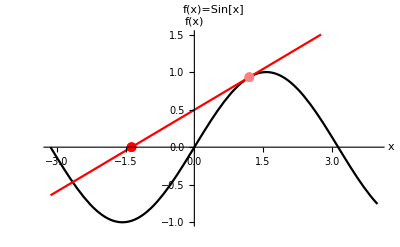

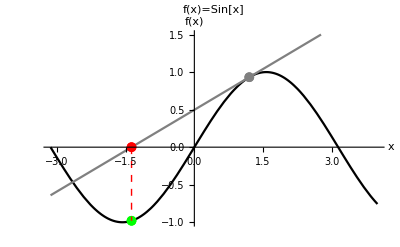

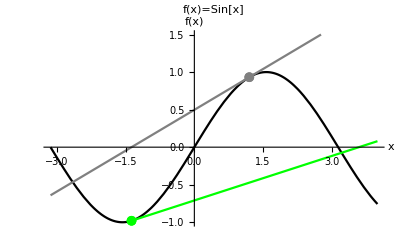

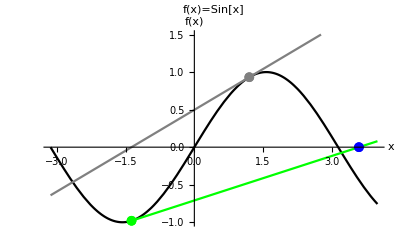

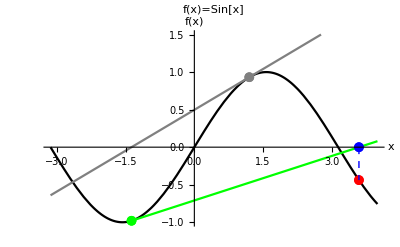

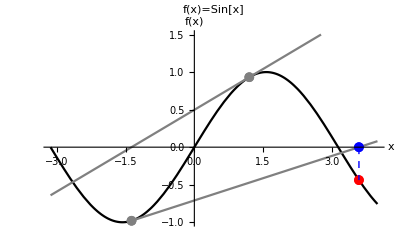

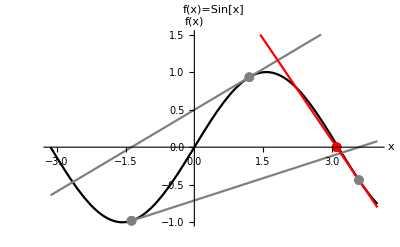

```mathematica
Clear
x0 = 1.2;
x1=x0-Sin[x0]/Cos[x0]//N
x2=x1-Sin[x1]/Cos[x1]//N
x3=x2-Sin[x2]/Cos[x2]//N
(*1*)
Plot[Sin[x],{x,-π,4},PlotStyle->{Black},PlotLabel->"f(x)=Sin[x]",AxesLabel->{"x","f(x)"},PlotRange->{{-π,4},{-1,1.5}}]
(*2*)
Show[Plot[Sin[x],{x,-π,4},PlotStyle->Black,PlotLabel->"f(x)=Sin[x]",AxesLabel->{"x","f(x)"},PlotRange->{{-π,4},{-1,1.5}}],ListPlot[{{1,Sin[1]}},PlotMarkers->{"●",8},PlotStyle->Red]]
(*3*)
Show[Plot[{Sin[x],Sin[x0]+Cos[x0]*(x-x0)},{x,-π,4},PlotStyle->{Black,Red},PlotLabel->"f(x)=Sin[x]",AxesLabel->{"x","f(x)"},PlotRange->{{-π,4},{-1,1.5}}],ListPlot[{{{x0,Sin[x0]}},{{x1,0}}},PlotMarkers->{{●,10},{●,10}},PlotStyle->{Pink,Red}]]
(*4*)
Show[Plot[{Sin[x],Sin[x0]+Cos[x0]*(x-x0)},{x,-π,4},PlotStyle->{Black,Gray},PlotLabel->"f(x)=Sin[x]",AxesLabel->{"x","f(x)"},PlotRange->{{-π,4},{-1,1.5}}],ListPlot[{{{x0,Sin[x0]}},{{x1,0}},{{x0-Sin[x0]/Cos[x0],Sin[x0-Sin[x0]/Cos[x0]]}}},PlotMarkers->{{●,10},{●,10},{●,10}},PlotStyle->{Gray,Red,Green}],Graphics[{Dashed,Red,Line[{{x1,0},{x1,Sin[x1]}}]}]]
(*5*)
Show[Plot[{Sin[x],Sin[x0]+Cos[x0]*(x-x0),Sin[x1]+Cos[x1]*(x-(x1))},{x,-π,4},PlotStyle->{Black,Gray,Green},PlotLabel->"f(x)=Sin[x]",AxesLabel->{"x","f(x)"},PlotRange->{{-π,4},{-1,1.5}}],ListPlot[{{{x0,Sin[x0]}},{{x0-Sin[x0]/Cos[x0],Sin[x0-Sin[x0]/Cos[x0]]}}},PlotMarkers->{{●,10},{●,10}},PlotStyle->{Gray,Green}]]
(*5*)
Show[Plot[{Sin[x],Sin[x0]+Cos[x0]*(x-x0),Sin[x1]+Cos[x1]*(x-(x1))},{x,-π,4},PlotStyle->{Black,Gray,Green},PlotLabel->"f(x)=Sin[x]",AxesLabel->{"x","f(x)"},PlotRange->{{-π,4},{-1,1.5}}],ListPlot[{{{x0,Sin[x0]}},{{x0-Sin[x0]/Cos[x0],Sin[x0-Sin[x0]/Cos[x0]]}},{{x2,0}}},PlotMarkers->{{●,10},{●,10},{●,10}},PlotStyle->{Gray,Green,Blue}]]
(*6*)
Show[Plot[{Sin[x],Sin[x0]+Cos[x0]*(x-x0),Sin[x1]+Cos[x1]*(x-(x1))},{x,-π,4},PlotStyle->{Black,Gray,Green},PlotLabel->"f(x)=Sin[x]",AxesLabel->{"x","f(x)"},PlotRange->{{-π,4},{-1,1.5}}],ListPlot[{{{x0,Sin[x0]}},{{x0-Sin[x0]/Cos[x0],Sin[x0-Sin[x0]/Cos[x0]]}},{{x2,0}},{{x2,Sin[x2]}}},PlotMarkers->{{●,10},{●,10},{●,10}},PlotStyle->{Gray,Green,Blue,Red,Red}],Graphics[{Dashed,Blue,Line[{{x2,0},{x2,Sin[x2]}}]}]]
(*6*)
Show[Plot[{Sin[x],Sin[x0]+Cos[x0]*(x-x0),Sin[x1]+Cos[x1]*(x-(x1))},{x,-π,4},PlotStyle->{Black,Gray,Gray},PlotLabel->"f(x)=Sin[x]",AxesLabel->{"x","f(x)"},PlotRange->{{-π,4},{-1,1.5}}],ListPlot[{{{x0,Sin[x0]}},{{x0-Sin[x0]/Cos[x0],Sin[x0-Sin[x0]/Cos[x0]]}},{{x2,0}},{{x2,Sin[x2]}}},PlotMarkers->{{●,10},{●,10},{●,10}},PlotStyle->{Gray,Gray,Blue,Red,Red}],Graphics[{Dashed,Blue,Line[{{x2,0},{x2,Sin[x2]}}]}]]
(*6*)
Show[Plot[{Sin[x],Sin[x0]+Cos[x0]*(x-x0),Sin[x1]+Cos[x1]*(x-(x1)),Sin[x2]+Cos[x2]*(x-(x2))},{x,-π,4},PlotStyle->{Black,Gray,Gray,Red},PlotLabel->"f(x)=Sin[x]",AxesLabel->{"x","f(x)"},PlotRange->{{-π,4},{-1,1.5}}],ListPlot[{{{x0,Sin[x0]}},{{x0-Sin[x0]/Cos[x0],Sin[x0-Sin[x0]/Cos[x0]]}},{{x2,Sin[x2]}},{{x3,0}}},PlotMarkers->{{●,10},{●,10},{●,10}},PlotStyle->{Gray,Gray,Gray,Red}]]
```

```mathematica
Clear[x1,x2]
Plot3D[{Exp[x1+x2]-x1,x1^2+x2},{x1,-1,1},{x2,-1,1}]
```

-Graphics3D-

```mathematica
Solve[{Exp[x1+x2]-x1==0,x1^2+x2==0}]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{ⅇ^(x1+x2)-x1==0,x1^2+x2==0}]

```mathematica
Solve[{D[Log[c]+Log[h]-h*Log[c],c]==0,
D[Log[c]+Log[h]-h*Log[c],c]==0},{c,h}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{h→1}}

```mathematica
NMaximize[{Log[c]+0.5*Log[h]+h*Log[1-c],h>0,c>0,c<1},{c,h}]
```

{-1.29572,{c→0.715332,h→0.397953}}

```mathematica
(({{Exp[x1]-2*Exp[x2]}, {x1+x2-3}})-({{D[Exp[x1]-2*Exp[x2],x1], D[Exp[x1]-2*Exp[x2],x2]}, {D[x1+x2-3,x1], D[x1+x2-3,x2]}}).({{x1-xx1}, {x2-xx2}}))/.{x1->0,x2->0}
```

{{-1+xx1-2 xx2},{-3+xx1+xx2}}

```mathematica
({{x1},{x2}}-(Inverse[({{Exp[x1], -2Exp[x2]}, {1, 1}})]).{{Exp[x1]-2*Exp[x2]},
{(x1+x2-3)}})/.{x1->0,x2->0}//N
(Inverse[({{Exp[x1], -2Exp[x2]}, {1, 1}})])/.{x1->2.333333,x2->0.6666667}
({{Exp[x1]-2*Exp[x2]},
{(x1+x2-3)}})/.{x1->2.333333,x2->0.6666667}
```

{{2.33333},{0.666667}}

{{0.0703843,0.27418},{-0.0703843,0.72582}}

{{6.41679},{-3.×10^-7}}

```mathematica
(-({{Exp[x1], -2Exp[x2]}, {1, 1}}).({{xx1-x1}, {xx2-x2}}))/.{x1->0,x2->0}
```

{{-xx1+2 xx2},{-xx1-xx2}}

```mathematica
{{-7/3},{-2/3}}//N
```

{{-2.33333},{-0.666667}}

```mathematica
Solve[{x1+x2==3,Exp[x1]-2*Exp[x2]==0},{x1,x2}]//N
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x1→1.84657,x2→1.15343}}

```mathematica
{x1+x2-3,Exp[x1]-2*Exp[x2]}/.{x1->0,x2->0}
```

{-3,-1}

```mathematica
viewpoint={-1,-1,1}
Show[Plot3D[x1+x2-3,{x1,-0.1,3},{x2,-0.1,3},PlotStyle->Blue,ViewPoint->{-1,-1,2}],ParametricPlot3D[{t,3-t,0},{t,-0.1,3},PlotStyle->RGBColor[1,0,0],ViewPoint->viewpoint],PlotLabel->"x_1+x2_2-3",AxesLabel->{"x_1","x_2","f(x_1,x_2)"}]
Show[Plot3D[Exp[x1]-2*Exp[x2],{x1,-0.1,3},{x2,-0.1,3},PlotStyle->Yellow,PlotLabel->"Exp[x_1]-2*Exp[x_2]",AxesLabel->{"x_1","x_2","f(x_1,x_2)"}],ParametricPlot3D[{t,t-Log[2],0},{t,-0.1,3},PlotStyle->RGBColor[1,0,0]],ViewPoint->viewpoint]
Show[Plot3D[x1+x2-3,{x1,-0.1,3},{x2,-0.1,3},PlotStyle->{Blue,Opacity[0.5]},ViewPoint->viewpoint,PlotLabel->"f(x_1,x_2)",AxesLabel->{"x_1","x_2","f(x_1,x_2)"}],ParametricPlot3D[{t,3-t,0},{t,-0.1,3},PlotStyle->RGBColor[1,0,0],ViewPoint->{-1,-1,2}],Plot3D[Exp[x1]-2*Exp[x2],{x1,-0.1,3},{x2,-0.1,3},PlotStyle->{Yellow,Opacity[0.7]}],ParametricPlot3D[{t,t-Log[2],0},{t,-0.1,3},PlotStyle->RGBColor[1,0,0]],ViewPoint->viewpoint]
Show[Plot3D[x1+x2-3,{x1,-0.1,3},{x2,-0.1,3},PlotStyle->{Blue,Opacity[0.5]},PlotLabel->"f(x_1,x_2)",AxesLabel->{"x_1","x_2","f(x_1,x_2)"}],ParametricPlot3D[{t,3-t,0},{t,-0.1,3},PlotStyle->RGBColor[1,0,0],ViewPoint->{1,3,2}],Plot3D[Exp[x1]-2*Exp[x2],{x1,-0.1,3},{x2,-0.1,3},PlotStyle->{Yellow,Opacity[0.7]}],ParametricPlot3D[{t,t-Log[2],0},{t,-0.1,3},PlotStyle->RGBColor[1,0,0]],ViewPoint->{1,3,2}]

Show[Show[Plot3D[x1+x2-3,{x1,-0.1,3},{x2,-0.1,3},PlotStyle->{Blue,Opacity[0.5]},PlotLabel->"f(x_1,x_2) and Approximations",AxesLabel->{"x_1","x_2","f(x_1,x_2)"}],ParametricPlot3D[{t,3-t,0},{t,-0.1,3},PlotStyle->RGBColor[1,0,0],ViewPoint->{1,3,2}],Plot3D[{Exp[x1]-2*Exp[x2],-1+x1-2 x2},{x1,-0.1,3},{x2,-0.1,3},PlotStyle->{Yellow,Opacity[0.7]}],ParametricPlot3D[{t,t-Log[2],0},{t,-0.1,3},PlotStyle->RGBColor[1,0,0]],ParametricPlot3D[{t,-0.5+t/2,0},{t,-0.1,3},PlotStyle->RGBColor[0,1,0]],ParametricPlot3D[{t,3-t,0},{t,-0.1,3},PlotStyle->{Thick,Dashed,RGBColor[0,1,0]}],ViewPoint->{1,3,2}],ListPointPlot3D[{{0,0,Exp[0]-2Exp[0]},{7/3,2/3,0}},PlotStyle->{Red,PointSize[0.05]}]]
```

{-1,-1,1}

-Graphics3D-

-Graphics3D-

-Graphics3D-

«3 more identical outputs»

```mathematica
Clear[x1,x2]
Solve[{-1+x1-2 x2==0,-3+x1+x2==0},{x1,x2}]//N
```

{{x1→2.33333,x2→0.666667}}

```mathematica
{{x1->7/3,x2->}}
```

Solve::argb: Solve called with 0 arguments; between 1 and 4 arguments are expected.

Solve[]

-Graphics3D-

-0.25

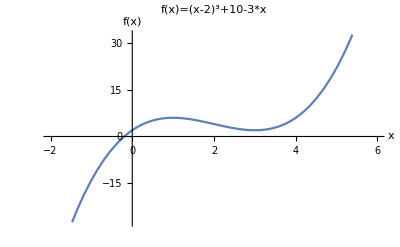

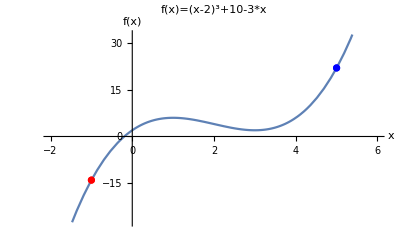

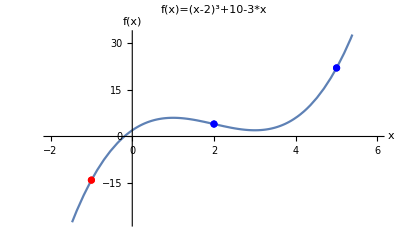

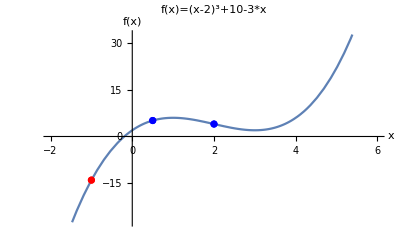

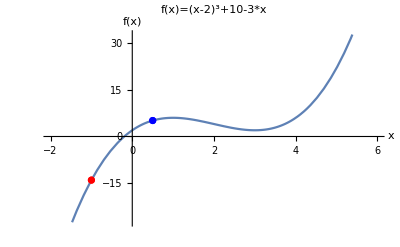

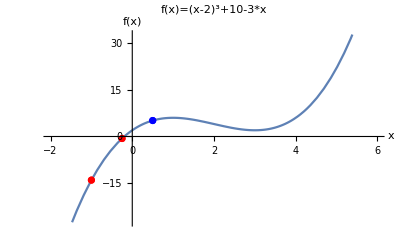

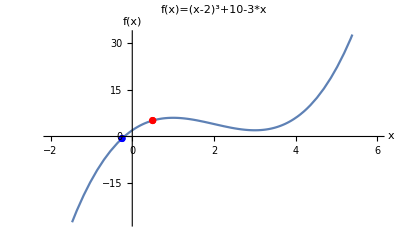

```mathematica
Clear[x]
F[x_]:=(x-2)^3+10-3*x
(-1+0.5)/2
Plot[F[x],{x,-2,6},PlotLabel->"f(x)=(x-2)^3+10-3*x",AxesLabel->{"x","f(x)"}]
Show[Plot[F[x],{x,-2,6},PlotLabel->"f(x)=(x-2)^3+10-3*x",AxesLabel->{"x","f(x)"}],ListPlot[{{{-1,F[-1]}},{{5,F[5]}}},PlotStyle->{Red,Blue}]]
Show[Plot[F[x],{x,-2,6},PlotLabel->"f(x)=(x-2)^3+10-3*x",AxesLabel->{"x","f(x)"}],ListPlot[{{{-1,F[-1]}},{{5,F[5]}},{{(-1+5)/2,F[(-1+5)/2]}}},PlotStyle->{Red,Blue,Blue}]]
Show[Plot[F[x],{x,-2,6},PlotLabel->"f(x)=(x-2)^3+10-3*x",AxesLabel->{"x","f(x)"}],ListPlot[{{{-1,F[-1]}},{{(-1+5)/2,F[(-1+5)/2]}},{{(-1+2)/2,F[(-1+2)/2]}}},PlotStyle->{Red,Blue,Blue}]]
Show[Plot[F[x],{x,-2,6},PlotLabel->"f(x)=(x-2)^3+10-3*x",AxesLabel->{"x","f(x)"}],ListPlot[{{{-1,F[-1]}},{{(-1+2)/2,F[(-1+2)/2]}}},PlotStyle->{Red,Blue,Blue}]]
Show[Plot[F[x],{x,-2,6},PlotLabel->"f(x)=(x-2)^3+10-3*x",AxesLabel->{"x","f(x)"}],ListPlot[{{{-1,F[-1]}},{{(-1+2)/2,F[(-1+2)/2]}},{{-1/4,F[-1/4]}}},PlotStyle->{Red,Blue,Red}]]
Show[Plot[F[x],{x,-2,6},PlotLabel->"f(x)=(x-2)^3+10-3*x",AxesLabel->{"x","f(x)"}],ListPlot[{{{(-1+2)/2,F[(-1+2)/2]}},{{-1/4,F[-1/4]}}},PlotStyle->{Red,Blue}]]
```

1/2 (-1+√5)

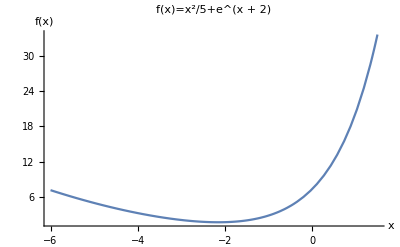

-5

1

-2.7082

-1.2918

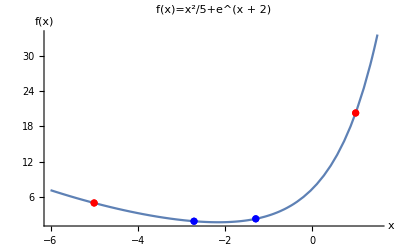

-5.

-1.2918

-3.58359

-2.7082

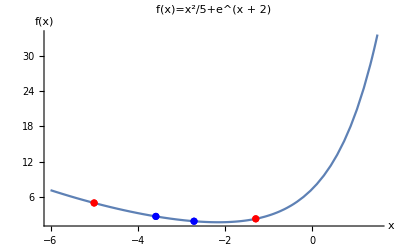

-3.58359

-1.2918

-2.7082

-2.16718

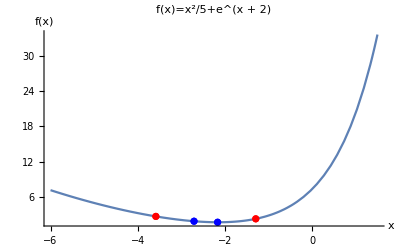

-2.7082

-1.2918

-2.16718

-1.83282

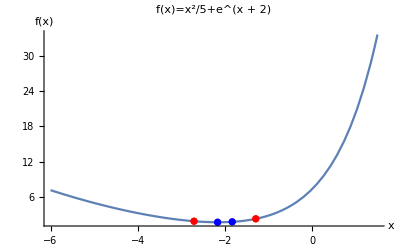

```mathematica
Clear[x]
ϕ=(-1+Sqrt[5])/2
F[x_]:=0.2*x^2+Exp[x+2]
Plot[F[x],{x,-6,1.5},PlotLabel->"f(x)=x^2/5+e^(x + 2)",AxesLabel->{"x","f(x)"},PlotRange->All]
a=-5
b=1
c=b-ϕ*(b-a)//N
d=a+ϕ*(b-a)//N
Show[Plot[F[x],{x,-6,1.5},PlotLabel->"f(x)=x^2/5+e^(x + 2)",AxesLabel->{"x","f(x)"},PlotRange->All],ListPlot[{{{a,F[a]}},{{b,F[b]}},{{c,F[c]}},{{d,F[d]}}},PlotStyle->{Red,Red,Blue,Blue}]]
a=Boole[(F[c]>F[d])]*c+Boole[(F[c]<F[d])]*a
b=Boole[(F[c]>F[d])]*b+Boole[(F[c]<F[d])]*d
c=b-ϕ*(b-a)//N
d=a+ϕ*(b-a)//N
Show[Plot[F[x],{x,-6,1.5},PlotLabel->"f(x)=x^2/5+e^(x + 2)",AxesLabel->{"x","f(x)"},PlotRange->All],ListPlot[{{{a,F[a]}},{{b,F[b]}},{{c,F[c]}},{{d,F[d]}}},PlotStyle->{Red,Red,Blue,Blue}]]
a=Boole[(F[c]>F[d])]*c+Boole[(F[c]<F[d])]*a
b=Boole[(F[c]>F[d])]*b+Boole[(F[c]<F[d])]*d
c=b-ϕ*(b-a)//N
d=a+ϕ*(b-a)//N
Show[Plot[F[x],{x,-6,1.5},PlotLabel->"f(x)=x^2/5+e^(x + 2)",AxesLabel->{"x","f(x)"},PlotRange->All],ListPlot[{{{a,F[a]}},{{b,F[b]}},{{c,F[c]}},{{d,F[d]}}},PlotStyle->{Red,Red,Blue,Blue}]]
a=Boole[(F[c]>F[d])]*c+Boole[(F[c]<F[d])]*a
b=Boole[(F[c]>F[d])]*b+Boole[(F[c]<F[d])]*d
c=b-ϕ*(b-a)//N
d=a+ϕ*(b-a)//N
Show[Plot[F[x],{x,-6,1.5},PlotLabel->"f(x)=x^2/5+e^(x + 2)",AxesLabel->{"x","f(x)"},PlotRange->All],ListPlot[{{{a,F[a]}},{{b,F[b]}},{{c,F[c]}},{{d,F[d]}}},PlotStyle->{Red,Red,Blue,Blue}]]
```

```mathematica
//N
```

0.618034

Boole[ⅇ^(2+3. False-2.56231 True-0.618034 (3.43769 False+3.43769 True))+2 (3. False-2.56231 True-0.618034 (3.43769 False+3.43769 True))^2>ⅇ^(2-0.437694 False-6. True+0.618034 (3.43769 False+3.43769 True))+2 (-0.437694 False-6. True+0.618034 (3.43769 False+3.43769 True))^2]